### Analyze colliding colony assay

```mathematica
(*function create a circle from three points that can be moved manually*)
createCircle[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=With[{a=Det[({{x1,y1,1},{x2,y2,1},{x3,y3,1}})],d=-Det[({{x1^2+y1^2,y1,1},{x2^2+y2^2,y2,1},{x3^2+y3^2,y3,1}})],e=Det[({{x1^2+y1^2,x1,1},{x2^2+y2^2,x2,1},{x3^2+y3^2,x3,1}})],f=-Det[({{x1^2+y1^2,x1,y1},{x2^2+y2^2,x2,y2},{x3^2+y3^2,x3,y3}})]},Circle[{-(d/(2 a)),-(e/(2 a))},Sqrt[(d^2+e^2)/(4 a^2)-f/a]]];
computeCircle[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=With[{a=Det[({{x1,y1,1},{x2,y2,1},{x3,y3,1}})],d=-Det[({{x1^2+y1^2,y1,1},{x2^2+y2^2,y2,1},{x3^2+y3^2,y3,1}})],e=Det[({{x1^2+y1^2,x1,1},{x2^2+y2^2,x2,1},{x3^2+y3^2,x3,1}})],f=-Det[({{x1^2+y1^2,x1,y1},{x2^2+y2^2,x2,y2},{x3^2+y3^2,x3,y3}})]},{{-(d/(2 a)),-(e/(2 a))},Sqrt[(d^2+e^2)/(4 a^2)-f/a]}];
createCircle[pts_]:={};
```

```mathematica
(*fit a circular arc to the interface between the colonies, connect the two colony centers with the line*)
sList2=DeleteDuplicates[StringSplit[#,{"=","-","("}][[2]]&/@FileNames[NotebookDirectory[]<>"F dox=*_c1+2*"]];
sList=ToExpression@StringReplace[#,","->"."]&/@sList2;
fns=GatherBy[FileNames[NotebookDirectory[]<>"F dox=*_c1+2*"],StringSplit[#,{"=","-","("}][[2]]&];
pointsdox=Table[{},{Length@sList}];
cancel=False;
For[i=1,i≤Length@sList,i++,{
pointsdox[[i]]=Table[{},{Length@fns[[i]]}];
For[j=1,j≤Length@fns[[i]],j++,{
If[cancel==True,Break[],{cancel=False;
img=Import@fns[[i,j]];
compRed=ComponentMeasurements[DeleteBorderComponents@Binarize[ColorSeparate[img][[1]],0.9],{"Centroid","Count"}];
compAll=ComponentMeasurements[DeleteBorderComponents@Binarize[img],{"Centroid","Count"}];
centerRed=Select[compRed,#[[2,2]]==Max@compRed[[All,2,2]]&][[1,2,1]],
centerAll=Select[compAll,#[[2,2]]==Max@compAll[[All,2,2]]&][[1,2,1]],
DynamicModule[{pts=(*Min[Max[0,#],1200]&/@*){centerAll-{0,200},centerAll,centerAll+{0,200},centerRed,centerRed+0 2(centerAll-centerRed)},c={}},If[!ChoiceDialog[{LocatorPane[Dynamic[pts],HighlightImage[img,Dynamic@Graphics[{Black,Thick,createCircle[pts[[1;;3]]],White,Thick,Line[pts[[4;;5]]](*,Point[Dynamic[pts]]*)}],ImageSize->{1200,Automatic},ImagePadding->0]],(*Button["Save and next",{pointsdox[[i,j]]=pts}],Button["Cancel",{Abort[],Dynamic}]*)Dynamic[pointsdox[[i,j]]=pts]},WindowTitle->"Colony #"<>ToString[j]<>" at concentration "<>sList2[[i]]<>":  Press OK or Enter to continue",WindowSize->All](*,UnsavedVariables->{pts}*),Abort[]]
]
}]
}]
}]
```

### Compute fitness differences

```mathematica
(*s[R] computes the fitness difference s from the ratio R of the radius of the circular arc of the interface and the distance between the colony centers*)
s[R_]:=(1-2 R+√(1+4 R^2))/(2 R)
fitnessDox=Table[0,{Length@sList}];
pointstemp=Select[#,#≠{}&]&/@pointsdox;
Monitor[For[i=1,i≤Length@sList,i++,{
(*fns=FileNames[NotebookDirectory[]<>"\\F*"<>sList2[[i]]<>"*c1+2.tif"],*)
fitnessDox[[i]]=Table[{},{Length@pointstemp[[i]]}],
For[j=1,j≤Length@fns[[i]],j++,{
img=Import@fns[[i,j]];
If[pointstemp[[i,j]],Continue[]],
{centerFit,radiusFit}=computeCircle[pointstemp[[i,j,1;;3]]],
distancesOfCenters=Sqrt@Total@((Flatten@Differences@pointstemp[[i,j,4;;5]])^2);
compRed=ComponentMeasurements[DeleteSmallComponents@DeleteBorderComponents@Binarize@ColorSeparate[ColorConvert[img,"LAB"]][[2]],{"Centroid","Count"}];
compAll=ComponentMeasurements[DeleteSmallComponents@FillingTransform@Dilation[DeleteBorderComponents@Binarize@GradientFilter[ColorSeparate[ColorConvert[img,"LAB"]][[1]],15],5],{"Centroid","Count"}];
centerRed=Select[compRed,#[[2,2]]==Max@compRed[[All,2,2]]&][[1,2,1]],
centerAll=Select[compAll,#[[2,2]]==Max@compAll[[All,2,2]]&][[1,2,1]],
norms={(centerRed-centerFit).(centerRed-centerFit),(centerAll-centerFit).(centerAll-centerFit)};
selectionDirection=If[norms[[1]]>norms[[2]],-1,+1];
selectiveDifference=selectionDirection*s[radiusFit/distancesOfCenters],
fitnessDox[[i,j]]=selectiveDifference;
}]

}],{j,i}]
```

### Plot

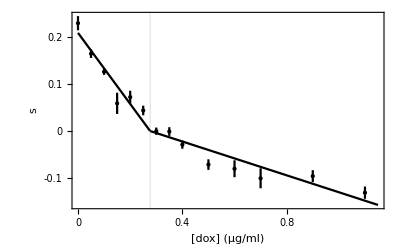

```mathematica
Needs["ErrorBarPlots`"]
f[x_,x0_]:=UnitStep[x0-x](A (x-x0))+UnitStep[x-x0](A1 (x-x0))
fit=FindFit[Transpose[{sList,(*-Min@fitnessDox[[{1,3,5,8}]]*)+Mean/@fitnessDox}],f[x,x0],{x0,A1,A},x];
fDox[x_]:=f[x,x0]/.fit
Show[ErrorListPlot[{Transpose[{Transpose[{sList,(*-Min@fitnessDox[[{1,3,5,8}]]*)+Mean/@fitnessDox}],ErrorBar[StandardDeviation@#/√(Length@#)]&/@fitnessDox}]},PlotStyle->{Black,White},Frame->{True,True,False,False},FrameLabel->{"[dox] (μg/ml)","s"},FrameTicks->myticksfull[-0.2,0.2,5,0,1.2,6],GridLines->{{0.2764338868458477},None}],Plot[fDox[x],{x,0,1.15},PlotStyle->Black],PlotRange->All]
```

### Data from published plot

```mathematica
fitnessDox={{0.3045800679514761,0.29028428965234876,0.20990103402465304,0.20228796680911887,0.19671152476224446,0.2231293001087679,0.1971374798216175,0.21672973719178043},{0.15373802996014846,0.16594555793892135,0.20339722374927477,0.1553395882938679,0.19099645653345043,0.1282314528068223,0.18217665682882933,0.14016364969308331},{0.12356371665284537,0.14240114062826584,0.11513864741285261,0.13794558942471355,0.15677554214649303,0.12625401390464444,0.14540443065388983,0.08291002507874069,0.1109803916706873,0.09058775868947722,0.14399646866378152,0.14138649778198523},{0.005869526900590435,0.1155695467190732,0.11789318168040118,0.13532492755714254,-0.11273806710402741,0.09706824934229412,0.013597994753659665,0.14381672970737605,-0.038478124589536054,0.05434257692069464,0.0696138605120427,0.10724112920892277},{0.09090523235181448,0.025978881926940416,0.04221432910444598,0.11573764139212013,-0.04220602759338073,0.09795161243727653,0.11048379628883648,0.11339359508505469,0.08521359550165339,0.11079158046435891,0.06260010991320111,0.055814557327238536},{0.11685549294959292,0.04698845403637918,0.03448372027535441,0.07454869821929538,0.046644735101039635,0.04619843338915696,0.050554032306618694,0.05460162215906935,0.04203304670667023,-0.03135864149308497,0.043068070946536634,0.0022482034344087835},{0.006243773573278414,0.012458906979094795,-0.014020455522604534,0.042980626916671164,-0.038325357103045854,0.0006591113878250605,0.006109299027917238,-0.0032890166826053634,-0.053576602092671365,-0.007801602408255868,0.03406191715964238,0.010504563924261672},{-0.013830345791330337,0.0478112202877819,0.04157515857927838,-0.01320924044468369,0.03096743564204425,0.018471286980563734,-0.07021739811081744,-0.012154219049548887,-0.016179891730508586,-0.012697044840292795,0.0006353276684394948,-0.014121130774078349},{-0.00721143227642931,-0.05582456124507938,-0.017502033349098032,-0.013567978271742295,0.0431694483354747,-0.060389434403952405,-0.006745573950909085,-0.030997242275475845,-0.04705885617973777,-0.04566382120835772,-0.058934291483659744,-0.04814991286219308},{-0.06057548372135459,-0.0009295331616863531,-0.06644463591692915,-0.11721544747026683,-0.10995335009256296,-0.0866447474881903,-0.13655937739418486,-0.017492020744453562,-0.07307191696654537,-0.0500830828886346,-0.08220757797535388,-0.058316803714783885},{-0.06774393744445013,-0.09456915009427608,-0.10697640792901304,-0.03168720025554558,0.012133563726593658,-0.09508733815706744,-0.09208795729805887,-0.06645419076856908,-0.021918602384313566,-0.1005387126041668,-0.21996680278978908},{-0.12950031409879392,-0.13341281921853745,-0.1665545305408286,-0.039144237165845405,0.06918762346174444,-0.06651978014486154,-0.08416248083074596,-0.0412337683282112,-0.13481504822197585,-0.14860051993068643,-0.21183100653174766,-0.1231106315555939},{-0.09396279621061311,-0.05697656547631006,-0.08214599189165202,-0.10055451512989623,-0.05504388341206871,-0.16165443337465432,-0.1917099752396741,-0.07472671940379465,-0.060836875438251725,-0.10863484311819827,-0.048170683502073326,-0.12095723737255022},{-0.14486637932415003,-0.10673923155832526,-0.21670980162389442,-0.19836709439986128,-0.07133715772662441,-0.1632198026660859,-0.08145549268032376,-0.11475772227465074,-0.11592321457329681,-0.09416325021744486,-0.11463078480645221,-0.1563751327818813}};
```

```mathematica
pointsdox={{{{630.,420.},{639.5,549.},{581.5,730.},{741.,536.},{515.5,540.}},{{696.,350.},{726.,525.},{695.,685.},{854.5,532.},{610.5,521.}},{{672.,357.},{707.5,570.},{666.,760.},{812.,563.},{604.5,546.}},{{625.5,333.},{648.5,536.},{596.5,733.},{750.5,526.},{545.5,525.}},{{662.5,350.},{675.5,521.},{655.5,668.},{813.,494.},{539.,488.}},{{685.5,386.},{691.5,554.},{653.5,711.},{577.,516.},{822.,531.}},{{690.5,300.},{711.,490.},{676.5,674.},{851.,473.},{616.5,468.}},{{574.5,364.},{621.,557.},{603.5,731.},{526.,563.},{746.,560.}}},{{{679.,410.},{687.,534.},{668.5,687.},{798.,520.},{581.5,523.}},{{697.5,357.},{717.,519.},{694.,687.},{832.5,510.},{631.5,511.}},{{729.5,386.},{749.5,528.},{726.,697.},{645.,531.},{855.5,545.}},{{660.5,421.},{666.,519.},{658.,634.},{779.5,519.},{533.,524.}},{{683.5,372.},{696.,516.},{672.,669.},{592.,504.},{809.5,514.}},{{644.,336.},{662.5,498.},{658.,629.},{548.,514.},{788.5,511.}},{{645.,344.},{668.5,503.},{652.,632.},{587.5,502.},{766.5,506.}},{{689.,366.},{699.5,523.},{684.5,651.},{598.,511.},{803.5,516.}}},{{{683.5,415.},{696.,543.},{690.5,656.},{793.5,538.},{600.,542.}},{{680.,375.},{691.5,518.},{675.5,667.},{585.,521.},{794.5,520.}},{{688.,365.},{704.,540.},{697.5,660.},{808.5,524.},{586.,531.}},{{700.5,400.},{706.5,519.},{694.,634.},{805.,513.},{613.,511.}},{{666.,344.},{683.5,516.},{665.,647.},{778.,514.},{593.,517.}},{{640.5,363.},{646.5,489.},{640.5,590.},{521.5,489.},{775.,487.}},{{676.5,555.},{665.,395.},{658.,689.},{585.,549.},{778.,554.}},{{716.,403.},{722.5,547.},{716.,667.},{825.5,540.},{613.,541.}},{{665.,344.},{674.,514.},{661.5,643.},{785.,506.},{573.5,497.}},{{676.5,355.},{687.,558.},{681.,629.},{773.5,509.},{598.,511.}},{{685.5,381.},{702.,530.},{694.,663.},{808.5,542.},{584.,538.}},{{676.5,363.},{696.,517.},{691.5,637.},{808.5,509.},{585.,518.}}},{{{660.5,391.},{666.2857142857143,883.5},{666.2857142857143,1083.5},{500.5,497.},{845.5,501.}},{{727.5,481.},{660.5,60.},{674.,835.},{591.,499.},{871.,513.}},{{586.,343.},{595.5,513.},{579.5,676.},{473.,511.},{716.,510.}},{{697.5,270.},{729.5,472.},{725.,635.},{604.5,497.},{858.,489.}},{{674.,517.},{670.5,415.},{657.,680.},{566.5,527.},{772.5,534.}},{{692.5,440.},{697.5,546.},{695.,636.},{574.5,564.},{817.5,565.}},{{675.5,431.},{673.,577.},{670.5,661.},{550.5,541.},{796.5,542.}},{{658.,392.},{668.5,525.},{659.,657.},{542.5,512.},{780.5,510.}},{{712.5,402.},{718.,536.},{717.,657.},{628.,549.},{823.5,548.}},{{653.5,396.},{655.5,639.},{658.,525.},{547.,533.},{773.5,525.}},{{707.5,320.},{707.5,474.},{694.,624.},{821.,468.},{593.,451.}},{{696.,363.},{703.,509.},{695.,649.},{569.,504.},{847.5,504.}}},{{{710.,384.},{717.,496.},{713.5,616.},{608.,497.},{829.,501.}},{{746.,447.},{748.,562.},{748.,607.},{869.5,518.},{633.5,514.}},{{628.,391.},{632.5,490.},{633.5,577.},{520.5,479.},{747.,466.}},{{682.,445.},{684.5,524.},{679.,634.},{813.,533.},{558.5,533.}},{{717.,475.},{720.5,569.},{720.5,673.},{607.,557.},{827.,563.}},{{712.5,369.},{712.5,524.},{694.,667.},{609.5,505.},{827.,516.}},{{709.,410.},{716.,519.},{711.,647.},{595.5,513.},{837.,520.}},{{662.5,403.},{668.5,546.},{654.5,685.},{571.,543.},{785.,548.}},{{680.,368.},{685.5,506.},{680.,619.},{572.5,491.},{805.,497.}},{{643.,319.},{655.5,424.},{655.5,568.},{550.5,439.},{772.5,437.}},{{699.5,386.},{697.5,526.},{694.,583.},{573.5,483.},{828.,491.}},{{668.5,439.},{676.5,568.},{676.5,680.},{573.5,564.},{785.,555.}}},{{{718.,351.},{710.,443.},{713.5,612.},{583.,476.},{852.5,482.}},{{717.,395.},{714.5,502.},{716.,609.},{584.,484.},{846.5,501.}},{{710.,133.},{697.5,474.},{699.5,602.},{548.,502.},{852.5,503.}},{{759.5,37.},{691.5,490.},{695.,614.},{580.5,486.},{817.5,487.}},{{735.5,105.},{700.5,474.},{699.5,607.},{574.5,498.},{838.5,496.}},{{754.,501.},{750.5,630.},{766.5,960.},{615.,546.},{889.5,558.}},{{738.,327.},{729.5,660.},{747.,867.},{610.5,497.},{853.5,501.}},{{763.,136.},{726.,517.},{733.,715.},{623.,492.},{857.,496.}},{{721.5,240.},{710.,501.},{719.,683.},{620.,502.},{815.5,506.}},{{735.5,265.},{743.5,410.},{746.,547.},{624.5,400.},{860.5,386.}},{{740.,196.},{728.5,395.},{734.5,663.},{609.5,483.},{855.5,474.}},{{727.5,121.},{729.5,506.},{731.,653.},{614.,531.},{852.5,528.}}},{{{672.,108.},{655.5,467.},{651.,604.},{548.,474.},{784.,473.}},{{680.,100.},{670.5,512.},{670.5,600.},{545.5,502.},{814.,510.}},{{668.5,156.},{691.5,501.},{696.,632.},{589.5,504.},{795.5,502.}},{{672.,83.},{689.,512.},{681.,657.},{813.,502.},{557.5,502.}},{{710.,297.},{702.,532.},{705.5,652.},{809.5,525.},{598.,526.}},{{666.,170.},{661.5,457.},{659.,604.},{768.,457.},{552.5,454.}},{{684.5,49.},{680.,440.},{676.5,591.},{535.5,489.},{818.5,487.}},{{666.,354.},{668.5,498.},{670.5,597.},{532.,498.},{813.,495.}},{{676.5,376.},{668.5,516.},{668.5,620.},{788.5,518.},{565.5,504.}},{{732.,105.},{706.5,487.},{699.5,614.},{544.5,473.},{886.,490.}},{{712.5,346.},{719.,509.},{719.,629.},{837.,505.},{599.,505.}},{{694.,417.},{689.,518.},{685.5,601.},{563.,499.},{825.5,514.}}},{{{697.5,247.},{684.5,533.},{682.,656.},{576.,503.},{800.,504.}},{{638.5,438.},{633.5,547.},{628.,621.},{490.,523.},{792.,532.}},{{689.,420.},{689.,534.},{685.5,644.},{552.5,523.},{839.5,527.}},{{623.,387.},{622.,526.},{623.,654.},{511.,517.},{744.5,517.}},{{742.5,435.},{734.5,583.},{732.,737.},{624.5,575.},{868.5,582.}},{{726.,343.},{714.5,521.},{698.5,689.},{614.,502.},{822.,520.}},{{699.5,312.},{687.,491.},{694.,636.},{598.,488.},{785.,489.}},{{706.5,358.},{699.5,518.},{695.,687.},{595.5,513.},{828.,519.}},{{718.,420.},{709.,567.},{704.,678.},{574.5,554.},{831.5,560.}},{{741.,383.},{736.5,533.},{734.5,668.},{616.5,518.},{853.5,519.}},{{657.,302.},{652.,502.},{648.5,638.},{514.5,494.},{805.,496.}},{{738.,366.},{733.,516.},{731.,652.},{626.5,495.},{842.,497.}}},{{{682.,384.},{681.,517.},{681.,632.},{563.,523.},{800.,520.}},{{711.,304.},{697.5,488.},{696.,598.},{565.5,483.},{834.,490.}},{{663.5,392.},{653.5,562.},{648.5,705.},{549.,520.},{777.,534.}},{{683.5,400.},{679.,519.},{676.5,615.},{549.,517.},{795.5,516.}},{{662.5,368.},{665.,480.},{663.5,583.},{544.5,479.},{791.,482.}},{{746.,95.},{704.,453.},{703.,582.},{569.,446.},{832.5,453.}},{{697.5,420.},{699.5,536.},{706.5,791.},{589.5,534.},{834.,533.}},{{681.,437.},{677.5,564.},{679.,687.},{592.,548.},{784.,554.}},{{728.5,377.},{716.,527.},{712.5,681.},{835.,535.},{603.5,521.}},{{691.5,413.},{684.5,534.},{684.5,675.},{586.,524.},{788.5,533.}},{{667.,444.},{665.,539.},{667.,650.},{820.,534.},{518.,545.}},{{691.5,399.},{689.,505.},{691.5,617.},{801.5,504.},{578.,501.}}},{{{675.5,356.},{679.,482.},{673.,617.},{579.5,477.},{792.,491.}},{{381.3907014681892,405.02365415986947},{381.5,605.},{381.3907014681892,805.0236541598695},{551.5,455.},{891.5,459.}},{{687.,356.},{695.,490.},{694.,609.},{592.,498.},{831.5,489.}},{{687.,321.},{697.5,489.},{685.5,621.},{584.,482.},{802.5,479.}},{{719.,430.},{724.,560.},{712.5,697.},{602.5,553.},{831.5,554.}},{{659.,468.},{663.5,597.},{658.,715.},{537.5,578.},{790.,572.}},{{636.,390.},{647.5,511.},{640.5,644.},{762.,504.},{540.,497.}},{{776.,409.},{773.5,503.},{768.,638.},{643.,514.},{924.,526.}},{{663.5,356.},{667.,531.},{659.,644.},{559.5,513.},{784.,516.}},{{679.,378.},{684.5,524.},{682.,651.},{574.5,517.},{807.,503.}},{{682.,324.},{685.5,466.},{677.5,599.},{559.5,469.},{816.5,474.}},{{685.5,436.},{689.,554.},{687.,657.},{570.,539.},{825.5,535.}}},{{{742.5,334.},{729.5,488.},{729.5,626.},{847.5,488.},{620.,474.}},{{682.,403.},{673.,521.},{677.5,649.},{574.5,525.},{775.,525.}},{{680.,466.},{687.,564.},{683.5,689.},{574.5,567.},{803.5,563.}},{{728.5,459.},{732.,578.},{732.,687.},{618.5,567.},{860.5,567.}},{{690.5,390.},{689.,512.},{689.,647.},{572.5,505.},{824.5,513.}},{{692.5,388.},{696.,526.},{685.5,663.},{572.5,520.},{818.5,527.}},{{601.5,458.},{610.5,623.},{601.5,757.},{725.,610.},{507.5,609.}},{{658.,365.},{665.,513.},{660.5,646.},{784.,511.},{561.,524.}},{{677.5,70.},{674.,496.},{666.,658.},{838.5,496.},{528.5,486.}},{{638.5,290.},{672.,551.},{670.5,674.},{543.5,553.},{808.5,542.}},{{696.,298.},{636.,562.},{652.,687.},{519.,554.},{747.,553.}}},{{{761.,196.},{684.5,509.},{684.5,637.},{557.5,517.},{787.5,525.}},{{739.,318.},{718.,465.},{720.5,609.},{594.5,469.},{824.5,489.}},{{698.5,363.},{675.5,523.},{691.5,711.},{567.5,523.},{806.,525.}},{{692.5,405.},{690.5,508.},{691.5,610.},{554.,513.},{823.5,511.}},{{663.5,361.},{658.,503.},{666.,657.},{549.,502.},{768.,501.}},{{746.,327.},{728.5,471.},{724.,697.},{603.5,453.},{839.5,473.}},{{783.,343.},{770.,504.},{777.,656.},{670.5,502.},{871.,496.}},{{719.,376.},{716.,525.},{719.,646.},{588.5,503.},{831.5,506.}},{{710.,395.},{700.5,510.},{704.,623.},{569.,501.},{824.5,509.}},{{728.5,341.},{710.,530.},{716.,645.},{571.,506.},{854.5,511.}},{{796.5,141.},{668.5,509.},{677.5,628.},{556.,497.},{799.,495.}},{{629.,393.},{626.5,540.},{638.5,656.},{488.,534.},{743.5,526.}}},{{{769.,102.},{691.5,490.},{719.,826.},{572.5,498.},{809.5,506.}},{{748.,257.},{729.5,472.},{735.5,720.},{613.,461.},{846.5,474.}},{{689.,398.},{679.,532.},{680.,661.},{554.,527.},{807.,536.}},{{694.,272.},{674.,490.},{704.,748.},{564.5,513.},{786.5,509.}},{{702.,361.},{691.5,532.},{713.5,953.},{550.5,528.},{830.5,538.}},{{1174.9166666666667,-177.91666666666663},{691.5,380.},{685.5,664.},{569.,498.},{798.,510.}},{{721.5,395.},{707.5,506.},{806.,834.},{611.5,497.},{806.,497.}},{{720.5,410.},{718.,536.},{724.,657.},{596.5,528.},{853.5,528.}},{{725.,105.},{688.,508.},{706.5,783.},{556.,502.},{809.5,508.}},{{707.5,361.},{697.5,498.},{706.5,637.},{594.5,495.},{802.5,495.}},{{725.,145.},{685.5,547.},{684.5,638.},{554.,520.},{822.,526.}},{{713.5,350.},{705.5,491.},{714.5,598.},{604.5,480.},{807.,483.}}},{{{705.5,372.},{685.5,539.},{689.,660.},{556.,524.},{821.,536.}},{{699.5,407.},{694.,520.},{696.,612.},{535.5,496.},{831.5,508.}},{{801.5,112.},{702.,446.},{710.,558.},{581.5,439.},{836.,445.}},{{777.,341.},{753.,531.},{763.,639.},{635.,512.},{886.,512.}},{{747.,118.},{689.,494.},{688.,613.},{566.5,487.},{805.,487.}},{{824.5,19.},{695.,464.},{748.,771.},{567.5,461.},{829.,462.}},{{687.,458.},{681.,569.},{724.,970.},{552.5,560.},{803.5,572.}},{{722.5,268.},{699.5,486.},{713.5,651.},{588.5,523.},{809.5,517.}},{{743.5,269.},{703.,526.},{707.5,641.},{598.,513.},{809.5,517.}},{{729.5,203.},{682.,542.},{702.,888.},{527.,530.},{842.,551.}},{{684.5,425.},{691.5,541.},{647.5,878.},{572.5,533.},{834.,528.}},{{775.,180.},{711.,511.},{722.5,642.},{586.,504.},{832.5,509.}}}};
pointstemp=Select[#,#≠{}&]&/@pointsdox;
```